```mathematica
ClearAll["Global`*"]
```

## AA 279 - PS 2 - Ellipsoids

#### Saving

```mathematica
NotebookDirectory[]
title="omega1";
savename[specific_]:=StringJoin[NotebookDirectory[],"figures\\",title,"_",specific,".png"]

savename["test"]
```

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_test.png

### Ellipsoids

```mathematica
energyEllipsoidAxes[t_,imom_]:=2 t/imom
momentumEllipsoidAxes[l_,imom_]:=l^2/imom^2

(*omega1 = {0.0873,0.0698,0.0524}, bound = 0.2*)
(*omega2 = 3 * omega1, bound = 3*0.2*)
(*omega3 = 5*{-0.0099,0.99995,-0.00004}, bound = 9*)
(*omega4 = 5*{0, 1, 0}, bound = 9*)

omegabounds=0.2
omegainital=Quantity[{0.0873,0.0698,0.0524},1/("Seconds")];
(*isat=Quantity[{4770.398,6313.894,7413.202},"Kilograms" ("Meters")^2];*)
isat=Quantity[{4770.398,6313.894,7413.202},"Kilograms" ("Meters")^2];
lvecstart=isat*omegainital;
lstart=Norm[lvecstart]

tstart=1/2 lvecstart.omegainital

(*tstart=Quantity[43.7365,"Joules"];
lstart=Quantity[720.1078,("Kilogram"*("Meters")^2)/("Seconds")];*)

energyaxes=UnitConvert[√energyEllipsoidAxes[tstart,isat]]
momentumaxes=UnitConvert[√momentumEllipsoidAxes[lstart,isat]]
```

0.2

720.108 kg m^2/s

43.7365 kg m^2/s^2

{0.135413 per second,0.117703 per second,0.108626 per second}

{0.150953 per second,0.114051 per second,0.0971386 per second}

```mathematica
Graphics3D[{{Orange,Specularity[White,10],Opacity[0.6],Ellipsoid[{0,0,0},QuantityMagnitude[energyaxes]]},
{Cyan,Specularity[White,10],Opacity[0.6],Ellipsoid[{0,0,0},QuantityMagnitude[momentumaxes]]}}
]
```

-Graphics3D-

```mathematica
ωvec={ωx,ωy,ωz};
ωvecunits=Quantity[ωvec,1/("Seconds")];
energyeq=(ωvecunits^2).(1/energyaxes^2)
momentumeq=(ωvecunits^2).(1/momentumaxes^2)
```

54.5357 ωx^2+72.1811 ωy^2+84.7485 ωz^2

43.8848 ωx^2+76.8775 ωy^2+105.978 ωz^2

```mathematica
(*energyeq-momentumeq

Solve[{energyeq-momentumeq==0,energyeq==1,momentumeq==1},ωvec]*)
```

```mathematica
noPolhodeContourPlot=ContourPlot3D[{energyeq==1,momentumeq==1},{ωx,-omegabounds,omegabounds},{ωy,-omegabounds,omegabounds},{ωz,-omegabounds,omegabounds},Mesh->None,ContourStyle->Opacity[0.8],PlotTheme->"Detailed",AxesLabel->{"ω_x","ω_y","ω_z"},MaxRecursion->3,PlotPoints->120,AxesStyle->Black]
Export[savename["ellipsoids_no_polhode"],noPolhodeContourPlot,ImageResolution->300]

polhodeContourPlot=ContourPlot3D[{energyeq==1,momentumeq==1},{ωx,-omegabounds,omegabounds},{ωy,-omegabounds,omegabounds},{ωz,-omegabounds,omegabounds},MeshFunctions->{Function[{ωx,ωy,ωz,f},energyeq-momentumeq]},MeshStyle->{{Thick,Black}},Mesh->{{0}},ContourStyle->Opacity[0.8],PlotTheme->"Detailed",AxesLabel->{"ω_x","ω_y","ω_z"},MaxRecursion->3,PlotPoints->60,AxesStyle->Black]
Export[savename["ellipsoids_with_polhode"],polhodeContourPlot,ImageResolution->300]
```

-Graphics3D-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_ellipsoids_no_polhode.png

-Graphics3D-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_ellipsoids_with_polhode.png

#### Solve Euler Equations

```mathematica
eulerode={
ωx'[t]==1/ix((iy-iz)ωy[t]ωz[t]-mx),
ωy'[t]==1/iy((iz-ix)ωx[t]ωz[t]-my),
ωz'[t]==1/iz((ix-iy)ωx[t]ωy[t]-mz)};
eulerodeparams=eulerode/.{mx->0,my->0,mz->0,ix->isat[[1]],iy->isat[[2]],iz->isat[[3]]};

starttime=0.0;
endtime=360.0;
initconds={
ωx[starttime]==QuantityMagnitude[omegainital[[1]]],
ωy[starttime]==QuantityMagnitude[omegainital[[2]]],
ωz[starttime]==QuantityMagnitude[omegainital[[3]]]}

fulleulerivp=Flatten[{eulerodeparams,initconds}]

eulersol=NDSolve[fulleulerivp,{ωx,ωy,ωz},{t,starttime,endtime}]


numericalsolplot=Plot[Evaluate[{ωx[t],ωy[t],ωz[t]}/.eulersol],{t,starttime,endtime},AxesLabel->{"Time [s]","ω [rad/s]"},AxesStyle->Black,FrameStyle->Black,PlotLabels->{"ω_x","ω_y","ω_z"}]

Export[savename["numerical_integration"],numericalsolplot,ImageResolution->300]
```

{ωx[0.]==0.0873,ωy[0.]==0.0698,ωz[0.]==0.0524}

{ωx'[t]==-0.230444 ωy[t] ωz[t],ωy'[t]==0.41857 ωx[t] ωz[t],ωz'[t]==-0.208209 ωx[t] ωy[t],ωx[0.]==0.0873,ωy[0.]==0.0698,ωz[0.]==0.0524}

{{ωx→InterpolatingFunction[…],ωy→InterpolatingFunction[…],ωz→InterpolatingFunction[…]}}

-Graphics-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_numerical_integration.png

```mathematica
polhodeParametric=ParametricPlot3D[Evaluate[{ωx[t],ωy[t],ωz[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black]

contourwithcalcpolhode=Show[noPolhodeContourPlot,polhodeParametric]

Export[savename["ellipsoids_with_calculated_polhode"],contourwithcalcpolhode,ImageResolution->300]
```

-Graphics3D-

-Graphics3D-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_ellipsoids_with_calculated_polhode.png

### 2D Projection Plots

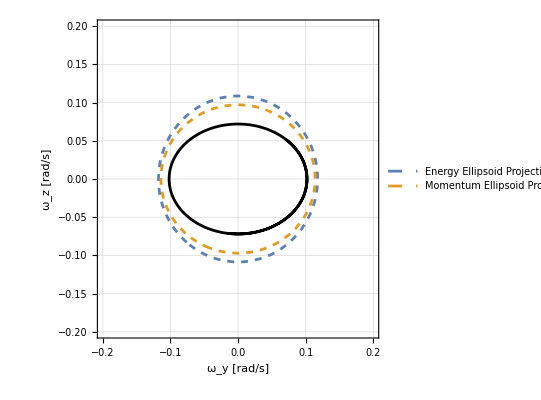

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_projected_polhode_yz.png

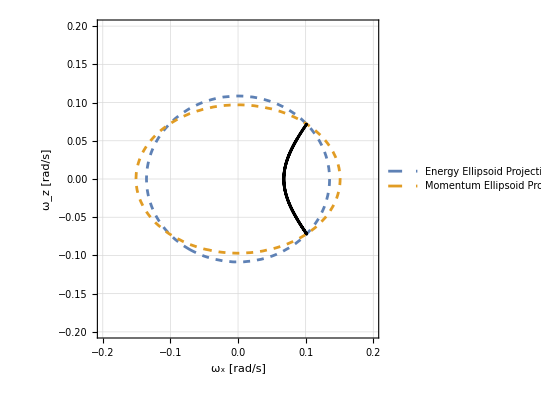

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_projected_polhode_xz.png

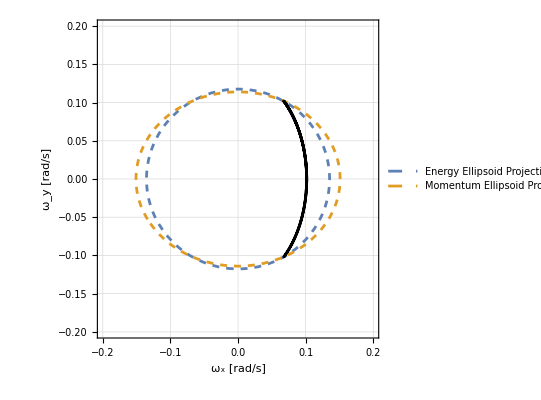

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_projected_polhode_xy.png

```mathematica
yz2dproj=Show[
ContourPlot[{Evaluate[energyeq/.ωx->0]==1,Evaluate[momentumeq/.ωx->0]==1},{ωy,-omegabounds,omegabounds},{ωz,-omegabounds,omegabounds},ContourStyle->Dashed,FrameLabel->{"ω_y [rad/s]","ω_z [rad/s]"},PlotTheme->"Detailed",GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->{"Energy Ellipsoid Projection","Momentum Ellipsoid Projection"},FrameStyle->Black],
ParametricPlot[Evaluate[{ωy[t],ωz[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black]
]
Export[savename["projected_polhode_yz"],yz2dproj,ImageResolution->300]

xz2dproj=Show[
ContourPlot[{Evaluate[energyeq/.ωy->0]==1,Evaluate[momentumeq/.ωy->0]==1},{ωx,-omegabounds,omegabounds},{ωz,-omegabounds,omegabounds},ContourStyle->Dashed,FrameLabel->{"ω_x [rad/s]","ω_z [rad/s]"},PlotTheme->"Detailed",GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->{"Energy Ellipsoid Projection","Momentum Ellipsoid Projection"},FrameStyle->Black],
ParametricPlot[Evaluate[{ωx[t],ωz[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black]
]
Export[savename["projected_polhode_xz"],xz2dproj,ImageResolution->300]

xy2dproj=Show[
ContourPlot[{Evaluate[energyeq/.ωz->0]==1,Evaluate[momentumeq/.ωz->0]==1},{ωx,-omegabounds,omegabounds},{ωy,-omegabounds,omegabounds},ContourStyle->Dashed,FrameLabel->{"ω_x [rad/s]","ω_y [rad/s]"},PlotTheme->"Detailed",GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->{"Energy Ellipsoid Projection","Momentum Ellipsoid Projection"},FrameStyle->Black],
ParametricPlot[Evaluate[{ωx[t],ωy[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black,PlotLabel->Automatic]
]
Export[savename["projected_polhode_xy"],xy2dproj,ImageResolution->300]
```

### Non-Dimensionalized

```mathematica
bΠ1=isat[[3]] Norm[omegainital]^2/tstart
bΠ2=isat[[3]] Norm[omegainital]/lstart

bΠ1prime=lstart^2/(2tstart isat[[3]])
bΠ2prime=(lstart Norm[omegainital])/tstart

ihatx=isat[[1]]/isat[[3]]
ihaty=isat[[2]]/isat[[3]]
```

2.58298

1.27083

0.799678

2.03251

0.6435

0.851709

0.300822 hatωx^2+0.156006 hatωy^2

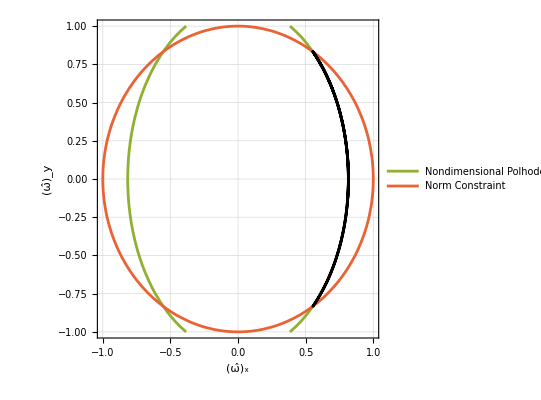

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\omega1_nondim_polhode.png

```mathematica
nondimellipseterm[ihat_,b1πp_]:=(1-b1πp-(ihat-b1πp)ihat)

nondimeq=nondimellipseterm[ihatx,bΠ1prime] hatωx^2+nondimellipseterm[ihaty,bΠ1prime] hatωy^2

nondimpolhode=Show[
ContourPlot[{0==0,0==0,nondimeq==1-bΠ1prime,hatωx^2+hatωy^2==1},{hatωx,-1,1},{hatωy,-1,1},PlotTheme->"Detailed",FrameLabel->{"(ω̂)_x","(ω̂)_y"},PlotLegends->{None,None,"Nondimensional Polhode","Norm Constraint"},GridLines->Automatic,GridLinesStyle->Dotted,FrameStyle->Black],
ParametricPlot[Evaluate[1/Norm[{ωx[t],ωy[t],ωz[t]}]{ωx[t],ωy[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black,PlotLabel->Automatic]
]

Export[savename["nondim_polhode"],nondimpolhode,ImageResolution->300]
```